## Green’s function

## Radiation Domination Kernel

```mathematica
(*The kernel may be defined in several ways*)
(*In line with the overleaf, I write it as the difference between two fast oscillating mode functions*)
(*These require 3 pieces functions as an input, which I write explicitly*)
ScaleFactor[t_,ω_]:=t^(2/(3(1+ω)));
```

```mathematica
(*For radiation domination, we simply use ω=1/3, such that the scale factor is equal to Sqrt[t]*)
ScaleFactor[t,1/3]
```

√t

```mathematica
(*Notation for below follows 1804.08577, which makes it easier to evaluate integral*)
```

```mathematica
(*Secondly, we have the mode functions acquired through the Green's analysis*)
(*In RD these are given by Spherical Bessel functions (To derive on mathematica)*)
```

```mathematica
g1[x_]:=x *SphericalBesselJ[0,x];
g2[x_]:=x *SphericalBesselY[0,x ];
```

```mathematica
(*Lastly, we have the source function*)
(*This is known analytically for RD*)
Source[x_,u_,v_]:=12/(u^3 v^3(x)^6)(18u*v*x^2 Cos[(u*x)/Sqrt[3]]Cos[(v*x)/Sqrt[3]]+(54-6(u^2+v^2)x^2+u^2 v^2 x^4)Sin[(u*x)/Sqrt[3]]Sin[(v*x)/Sqrt[3]]+2Sqrt[3]u*x(v^2 x^2-9)Cos[(u*x)/Sqrt[3]]Sin[(v*x)/Sqrt[3]]+2Sqrt[3]v*x(u^2 x^2-9)Sin[(u*x)/Sqrt[3]]Cos[(v*x)/Sqrt[3]]);
```

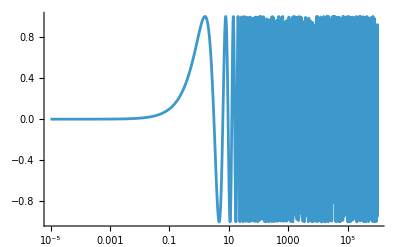

```mathematica
(*We are integrating these functions from 0 to Infty*)
(*Let's plot these functions for a better understanding of whats going into the integral*)
(*Remember, the real reason we are doing this is because we want to extend this to a general EoS scenario and figure out what part of Tada san's code is computationally expensive*)
LogLinearPlot[g1[x],{x,10^-5,10^6}]
```

```mathematica
(*Above follows y=x for x<1, then osciallates*)
```

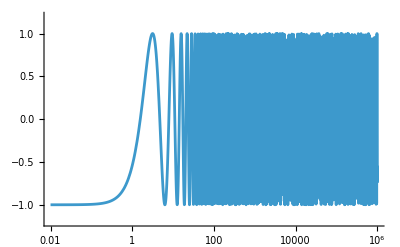

```mathematica
LogLinearPlot[g2[x],{x,10^-2,10^6},PlotRange->{-1.2,1.2}]
```

```mathematica
(*{u,v} integrals have limits {{Abs[1-v],1+v},{0,Infty}}*)
```

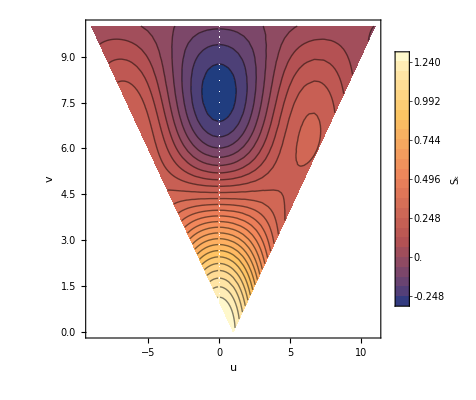

```mathematica
Quiet[ContourPlot[Source[1,u,v],{u,1-10,1+10},{v,0,10},Contours->25,PlotLegends->BarLegend[Automatic,LegendLabel->"S_k"],FrameLabel->{"u","v"},RegionFunction->Function[{u,v},1-v<u<1+v]]]
```

```mathematica
(*Let's begin with the positive integral, and use (a(η̃))/(a(η))=(η̃)/η*)
(*This corresponds to Subscript[I, 2] in the overleaf*)
RDintegral1[u_,v_]:=NIntegrate[x*g1[x]*Source[x,u,v],{x,0,Infinity}]
```

```mathematica
(*This corresponds to Subscript[I, 1] in the overleaf*)
RDintegral2[u_,v_]:=NIntegrate[x*g2[x]*Source[x,u,v],{x,0,Infinity}]
```

```mathematica
ContourPlot[RDintegral1[u,v],{u,1-10,1+10},{v,0,10},Contours->25,PlotLegends->BarLegend[Automatic,LegendLabel->"I_2"],FrameLabel->{"u","v"},RegionFunction->Function[{u,v},1-v<u<1+v]]
```

$Aborted

```mathematica
ContourPlot[RDintegral2[u,v],{u,1-10,1+10},{v,0,10},Contours->25,PlotLegends->BarLegend[Automatic,LegendLabel->"I_1"],FrameLabel->{"u","v"},RegionFunction->Function[{u,v},1-v<u<1+v]]
```

## Kernel change of variables (u,v) -> (s,t)

```mathematica
(*This is known analytically for RD*)
Source[x_,u_,v_]:=12/(u^3 v^3(x)^6)(18u*v*x^2 Cos[(u*x)/Sqrt[3]]Cos[(v*x)/Sqrt[3]]+(54-6(u^2+v^2)x^2+u^2 v^2 x^4)Sin[(u*x)/Sqrt[3]]Sin[(v*x)/Sqrt[3]]+2Sqrt[3]u*x(v^2 x^2-9)Cos[(u*x)/Sqrt[3]]Sin[(v*x)/Sqrt[3]]+2Sqrt[3]v*x(u^2 x^2-9)Sin[(u*x)/Sqrt[3]]Cos[(v*x)/Sqrt[3]]);
```

```mathematica
SourceST[x_,s_,t_]:=Source[x,(t+s+1)/2,(t-s+1)/2];
```

```mathematica
SourceST[x,s,t]
```

1/((1-s+t)^3 (1+s+t)^3 x^6)768 (9/2 (1-s+t) (1+s+t) x^2 Cos[((1-s+t) x)/(2 √3)] Cos[((1+s+t) x)/(2 √3)]+√3 (1+s+t) x (-9+1/4 (1-s+t)^2 x^2) Cos[((1+s+t) x)/(2 √3)] Sin[((1-s+t) x)/(2 √3)]+√3 (1-s+t) x (-9+1/4 (1+s+t)^2 x^2) Cos[((1-s+t) x)/(2 √3)] Sin[((1+s+t) x)/(2 √3)]+(54-6 (1/4 (1-s+t)^2+1/4 (1+s+t)^2) x^2+1/16 (1-s+t)^2 (1+s+t)^2 x^4) Sin[((1-s+t) x)/(2 √3)] Sin[((1+s+t) x)/(2 √3)])

## Φ_k Bardeen ODE

```mathematica
(*Assuming RD => Subscript[c, s]^2=ω=1/3, a(η)=η, H(η)=1/η*)
DSolve[Φ''[η]+4/η Φ'[η]+k^2/3 Φ[η]==0,Φ[η],η]
```

{{Φ[η]→(3^(1/4) √(2/π) C[2] (-(√3 Cos[(k η)/(√3)])/(k η)-Sin[(k η)/(√3)]))/(η^(3/2) √(k η))+(3^(1/4) √(2/π) C[1] (-Cos[(k η)/(√3)]+(√3 Sin[(k η)/(√3)])/(k η)))/(η^(3/2) √(k η))}}

```mathematica
(*Same as above, imposing a boundary condition*)
DSolve[{Φ''[η]+4/η Φ'[η]+k^2/3 Φ[η]==0,Φ[0]==1},Φ[η],η]
```

{{Φ[η]→-(9 (k η Cos[(k η)/(√3)]-√3 Sin[(k η)/(√3)]))/(k^(5/2) η^(5/2) √(k η))}}

```mathematica
(*x=k*η*)
```

```mathematica
ΦRD[x_]:=9/x^3(√3 Sin[x/(√3)]-x*Cos[x/(√3)]);
```

```mathematica
(*This matches https://arxiv.org/pdf/1804.08577*)
```

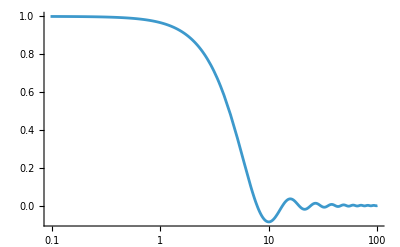

```mathematica
LogLinearPlot[ΦRD[x],{x,0,100},PlotRange->All]
```

```mathematica
(*Next, Subscript[c, s]^2(=c^2),ω as variables (note: we have not promoted them to functions of \eta (yet)), keeping H=1/(\eta)*)
```

```mathematica
DSolve[{Φ''[η]+(3(1+c^2))/η Φ'[η]+(c^2 k^2+3/η^2(c^2-ω))Φ[η]==0(*,Φ[0]==1,Φ'[0]==0*)},Φ[η],η]
```

{{Φ[η]→η^(1/2 (-2-3 c^2)) BesselJ[1/2 √(4+9 c^4+12 ω),c k η] C[1]+η^(1/2 (-2-3 c^2)) BesselY[1/2 √(4+9 c^4+12 ω),c k η] C[2]}}

```mathematica
(*This doens't seem to like the initial condition Φ[0]==1, or any initial conditions for that matter*)
```

```mathematica
Φ[k_,c_,w_,η_]:=η^((-2-3 c^2)/2)(c1*BesselJ[(√(4+9 c^4+12w))/2,c*k*η]+c2*BesselY[(√(4+9 c^4+12w))/2,c*k*η]);
```

```mathematica
(*Does NDSolve fix the issue? Nope, different problems*)
NDSolve[{Φ''[η]+(3(1+c^2))/η Φ'[η]+(c^2 k^2+3/η^2(c^2-ω))Φ[η]==0,Φ[0]==1,Φ'[0]==0},Φ,{η,1,500}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. (1+c^2) ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.^2 encountered.

NDSolve::ndnum: Encountered non-numerical value for a derivative at η == 0..

NDSolve[{(c^2 k^2+(3 (c^2-ω))/η^2) Φ[η]+(3 (1+c^2) Φ'[η])/η+Φ''[η]==0,Φ[0]==1,Φ'[0]==0},Φ,{η,1,500}]

## Source from Bardeen solution

```mathematica
(*Let's try and recover the source from https://arxiv.org/pdf/1804.08577 first*)
(*Assuming k<<Subscript[k, 1],Subscript[k, 2] we can approximate Subscript[k, 1]=Subscript[k, 2]*)
(*=>*)
SRD[k_,η_]:=2 ΦRD[k*η]^2+(ΦRD[k*η]+η*ΦRD'[k*η])^2;
```

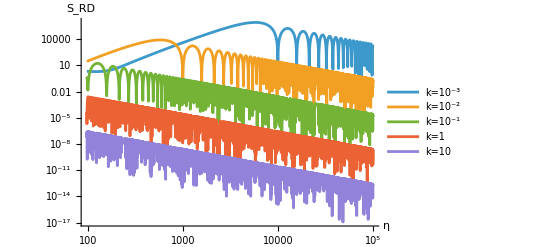

```mathematica
LogLogPlot[{SRD[10^-3,η],SRD[10^-2,η],SRD[10^-1,η],SRD[10^0,η],SRD[10,η]},{η,0,10^5},PlotRange->All,PlotLegends->{"k=10^-3","k=10^-2","k=10^-1","k=1","k=10"},AxesLabel->{"η","S_RD"}]
```

```mathematica
Simplify[SRD[k,η]]
```

(9 (18 k^2 (k η Cos[(k η)/(√3)]-√3 Sin[(k η)/(√3)])^2+(-3 (-3+k) k η Cos[(k η)/(√3)]+√3 (-9+3 k+k^2 η^2) Sin[(k η)/(√3)])^2))/(k^8 η^6)

```mathematica
(*This should match https://arxiv.org/pdf/1804.08577 first, assuming u=v (in their notation)*)
SRDKohri[x_,u_,v_]:=12/(u^3 v^3(x)^6)(18u*v*x^2 Cos[(u*x)/Sqrt[3]]Cos[(v*x)/Sqrt[3]]+(54-6(u^2+v^2)x^2+u^2 v^2 x^4)Sin[(u*x)/Sqrt[3]]Sin[(v*x)/Sqrt[3]]+2Sqrt[3]u*x(v^2 x^2-9)Cos[(u*x)/Sqrt[3]]Sin[(v*x)/Sqrt[3]]+2Sqrt[3]v*x(u^2 x^2-9)Sin[(u*x)/Sqrt[3]]Cos[(v*x)/Sqrt[3]]);
```

```mathematica
Simplify[SRDKohri[k*η,u,u]]
```

(6 (54+6 k^2 u^2 η^2+k^4 u^4 η^4-(54-30 k^2 u^2 η^2+k^4 u^4 η^4) Cos[(2 k u η)/(√3)]+4 √3 k u η (-9+k^2 u^2 η^2) Sin[(2 k u η)/(√3)]))/(k^6 u^6 η^6)